```mathematica
SetDirectory[NotebookDirectory[]];
fMean[x_,α_,β_,y0_]:=(ⅇ^(x α) y0)/(1-y0 β+ⅇ^(x α) y0 β)
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,0.002],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1,PlotRange->{Automatic,{0,400}}];
aPlot2=Plot[PDF[NormalDistribution[0,0.012],x],{x,-0.03,0.03},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1,PlotRange->{Automatic,{0,200}}];
aPlot3=Plot[PDF[NormalDistribution[0,0.01],x],{x,-0.03,0.03},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1,PlotRange->{Automatic,{0,200}}];
aPlot4=Plot[PDF[NormalDistribution[0,0.003],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1,PlotRange->{Automatic,{0,400}}];
```

```mathematica
g1=Show[Plot[fMean[x,0.5,0.05,5],{x,0,10},ImageSize->600,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameTicks->None,PlotStyle->Directive[Thick,Black],PlotRange->{{0.5,8},{0,23}},FrameLabel->{"Time","Quantity"}],Graphics[Inset[Rotate[aPlot2,3Pi /2],{2.2,fMean[1.3,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3Pi /2],{4.2,fMean[3.3,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3Pi /2],{6.2,fMean[5.3,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot4,3Pi /2],{8.2,fMean[7.3,0.5,0.05,5]}]]]
```

-Graphics-

```mathematica
fGenerateY1[sigma__]:=Block[{lX =Table[x,{x,{1.2,3.2,5.2, 7.2}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Table[{lX[[i]],fYGenerate[lX[[i]],0.5,0.05,5,sigma[[i]]]},{i,1,Length@lX,1}]]
```

```mathematica
data=Table[fGenerateY1[{1,2.5,2,1.5}],{i,1,4,1}];
```

```mathematica
g2=Labeled[Show[g1,ListPlot[data,PlotStyle->Blue,PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],FrameLabel->None,ImageSize->600,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},FrameTicks->None,PlotRange->{{1,8},{0,23}},FrameLabel->{"Time","Quantity"}]],"A.", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

-Graphics-A.

```mathematica
fLogLikelihood[lX_,lY_,α_,β_,y0_,σ_]:=Block[{lpred=fMean[#,α,β,y0]&/@lX,resid},resid=lY-lpred;LogLikelihood[NormalDistribution[0,σ],resid]]
fPrior[α_,β_,y0_,σ_]:=If[Total[If[#<0,1,0]&/@{α,β,y0,σ}]>0,0,1]
```

```mathematica
fStep[α_,β_,y0_,σ_,sigmaa_,sigmab_,sigmay0_,sigmasigma_]:=RandomVariate[MultinormalDistribution[{α,β,y0,σ},DiagonalMatrix[{sigmaa,sigmab,sigmay0,sigmasigma}]],1][[1]]
fStepAndAccept[lX_,lY_,α_,β_,y0_,σ_,sigmaa_,sigmab_,sigmay0_,sigmasigma_]:=Block[{lparams=fStep[α,β,y0,σ,sigmaa,sigmab,sigmay0,sigmasigma],u=RandomReal[],a1,b1,y1,σ1},a1=lparams[[1]];b1=lparams[[2]];y1=lparams[[3]];
σ1=lparams[[4]];
If[Exp[fLogLikelihood[lX,lY,a1,b1,y1,σ1] -fLogLikelihood[lX,lY,α,β,y0,σ] ] fPrior[a1,b1,y1,σ1] / fPrior[α,β,y0,σ]>u,{a1,b1,y1,σ1},{α,β,y0,σ}]]
fMCMC[numsteps_Integer,lX_,lY_,α_,β_,y0_,σ_,sigmaa_,sigmab_,sigmay0_,sigmasigma_]:=NestList[fStepAndAccept[lX,lY,#[[1]],#[[2]],#[[3]],#[[4]],sigmaa,sigmab,sigmay0,sigmasigma]&,{α,β,y0,σ},numsteps]
```

```mathematica
lX =Table[x,{x,0,10,0.5}];
lY=fYGenerate[#,0.5,0.05,5,3]&/@lX;
res=fMCMC[10000,lX,lY,0.5,0.05,5,3,0.1,0.005,0.5,0.3];
res1=DeleteDuplicates[res];
```

```mathematica
fRandomObservation[x_,α_,β_,y0_,jitter_]:=Block[{x1=RandomVariate[NormalDistribution[x,jitter],{1}][[1]]},{x1,fMean[x1,α,β,y0]}]
```

```mathematica
data=Table[fGenerateY[],{i,1,10,1}];
obs=Flatten@ConstantArray[{1.2,3.2,5.2, 7.2},50];
```

```mathematica
predata=Table[fRandomObservation[obs[[i]],res1[[i,1]],res1[[i,2]],res1[[i,3]],0.1],{i,1,16,1}];
```

```mathematica
g1a=Table[Show[Plot[fMean[x,res1[[i,1]],res1[[i,2]],res1[[i,3]]],{x,0,10},PlotStyle->Opacity[0.7,Black],FrameLabel->None,ImageSize->800,FrameTicks->None,PlotRange->{{0,8},{0,23}},FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}]],{i,1,16,1}];
g1b=Table[ListPlot[{predata[[i]]},PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],FrameLabel->None,ImageSize->800,FrameTicks->None,PlotRange->{Full,{0,23}},FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}],{i,1,16,1}];
```

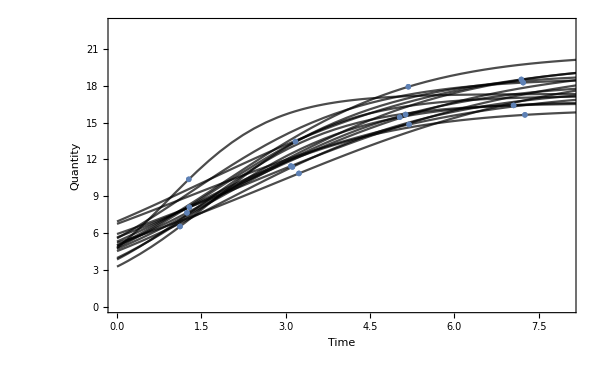
-Graphics-B.

```mathematica
g3=Labeled[Show[g1a,g1b,ImageSize->600,FrameLabel->{"Time","Quantity"},FrameStyle->Directive[Black,20,Thick]],"B.", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

```mathematica
g2=Labeled[Show[g1,ListPlot[predata,PlotStyle->Blue,PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],FrameLabel->None,ImageSize->600,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},FrameTicks->None,PlotRange->{{1,8},{0,23}},FrameLabel->{"Time","Quantity"}]],"A.", {{Top,Left}},LabelStyle->{Black,FontSize->20}]
```

-Graphics-A.

```mathematica
gFinal=GraphicsRow[{g2,g3},ImageSize->1300]
```

-Graphics-

```mathematica
Export["../figures/data_generation.pdf",gFinal]
```

../figures/data_generation.pdf